## Question 1

### Part A

```mathematica
P := ({{0.45, 0.35, 0.20}, {0.36, 0.34, 0.30}, {0.25, 0.65, 0.1}})
```

### Part B

```mathematica
outcomes := {{"Day", "Sunny", "Rainy", "Overcast"}}
For[day= 0, day<=5, day++,
AppendTo[
outcomes,
{
day,
({{1, 0, 0}}).MatrixPower[P,day]//MatrixForm//TraditionalForm,
({{0, 1, 0}}).MatrixPower[P,day]//MatrixForm//TraditionalForm,
({{0, 0, 1}}).MatrixPower[P,day]//MatrixForm//TraditionalForm
}]
]
Grid[outcomes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Day | Sunny | Rainy | Overcast
0 | (1. | 0. | 0.) | (0. | 1. | 0.) | (0. | 0. | 1.)
1 | (0.45 | 0.35 | 0.2) | (0.36 | 0.34 | 0.3) | (0.25 | 0.65 | 0.1)
2 | (0.3785 | 0.4065 | 0.215) | (0.3594 | 0.4366 | 0.204) | (0.3715 | 0.3735 | 0.255)
3 | (0.370415 | 0.410435 | 0.21915) | (0.369906 | 0.406834 | 0.22326) | (0.365385 | 0.422765 | 0.21185)
4 | (0.369231 | 0.411641 | 0.219129) | (0.368733 | 0.41291 | 0.218357) | (0.369581 | 0.409327 | 0.221092)
5 | (0.369127 | 0.411622 | 0.219251) | (0.369167 | 0.411378 | 0.219455) | (0.368942 | 0.412234 | 0.218824)

```mathematica
verdict :={
{"Day", "Sunny", "Rainy", "Overcast"},
{"0", "Sunny", "Rainy", "Rainy"},
{"1","Sunny","Sunny","Rainy"},
{"2","Rainy","Rainy","Rainy"},
{"3","Rainy","Rainy","Rainy"},
{"4","Rainy","Rainy","Rainy"},
{"5","Rainy","Rainy","Rainy"}
}
Grid[verdict,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Day | Sunny | Rainy | Overcast
0 | Sunny | Rainy | Rainy
1 | Sunny | Sunny | Rainy
2 | Rainy | Rainy | Rainy
3 | Rainy | Rainy | Rainy
4 | Rainy | Rainy | Rainy
5 | Rainy | Rainy | Rainy

### Part C

```mathematica
outcomes := {{"Day", "Sunny", "Rainy", "Overcast"}}
For[day= 0, day<=5, day++,
AppendTo[
outcomes,
{
day,
({{1, 0, 0}}).MatrixPower[P,day].({{1}, {2}, {3}})//MatrixForm//TraditionalForm,
({{0, 1, 0}}).MatrixPower[P,day].({{1}, {2}, {3}})//MatrixForm//TraditionalForm,
({{0, 0, 1}}).MatrixPower[P,day].({{1}, {2}, {3}})//MatrixForm//TraditionalForm
}]
]
Grid[outcomes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Day | Sunny | Rainy | Overcast
0 | (1.) | (2.) | (3.)
1 | (1.75) | (1.94) | (1.85)
2 | (1.8365) | (1.8446) | (1.8835)
3 | (1.84874) | (1.85335) | (1.84647)
4 | (1.8499) | (1.84962) | (1.85151)
5 | (1.85012) | (1.85029) | (1.84988)

## Question 2

```mathematica
X:=DiscreteMarkovProcess[{0.369, 0.4117, 0.2193},
{{0.45,0.35,0.2},
{0.36,0.34,0.30},
{0.25,0.65,0.1}}]
```

```mathematica
X:=DiscreteMarkovProcess[{1, 0, 0},
{{0.45,0.35,0.2},
{0.36,0.34,0.30},
{0.25,0.65,0.1}}]
```

```mathematica
PDF[X[3],k]//PiecewiseExpand
```

Piecewise[{{0.21915, k==3}, {0.370415, k==1}, {0.410435, k==2}, {0, True}}]

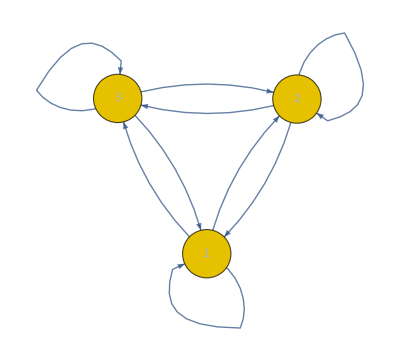

```mathematica
Graph[X]
```

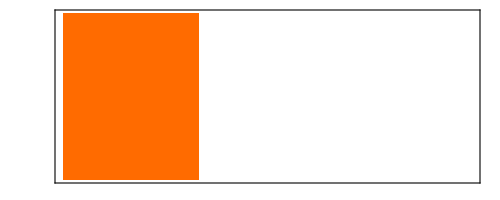
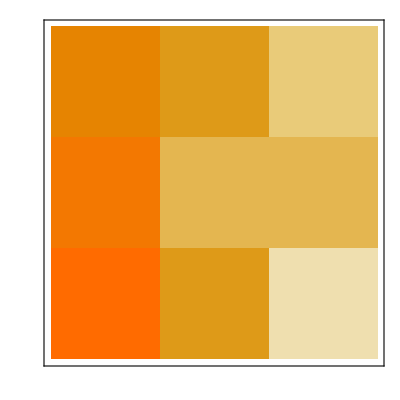
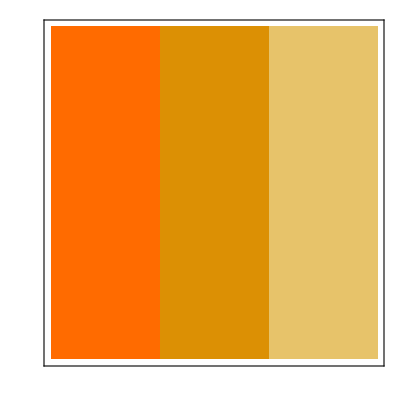
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0.818182,0.333333,0.111111}
HoldingTimeVariance | {1.4876,0.444444,0.123457}
Structural Properties | 
CommunicatingClasses | {1,2,3}
RecurrentClasses | {1,2,3}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[X]
```